# Pêndulo livre sem controlo, teste numérico usando stormer verlet e Runge-kutta

```mathematica
ClearAll["Global`*"]
ClearAll[Subscript]
ClearAll[Derivative]
```

## Contas teóricas

### Lagrangeano do Pêndulo esférico

```mathematica
L=1/2(θ'[t]^2+Sin[θ[t]]^2  ϕ'[t]^2)-Subscript[ω, 0]^2 Cos[θ[t]]
```

-Cos[θ[t]] ω_0^2+1/2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)

### Equação de movimento

```mathematica
D[D[L,θ'[t]],t]-D[L,θ[t]]/.A
```

ReplaceAll::reps: {A} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Sin[θ[t]] ω_0^2-Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+θ''[t]/.A

### Condição de conservação

```mathematica
A={ϕ'[t]->C/Sin[θ[t]]^2}
```

{ϕ'[t]→C Csc[θ[t]]^2}

### Hamiltoniano

```mathematica
H=θ'[t] D[L,θ'[t]]+ϕ'[t] D[L,ϕ'[t]]-L/.A/.θ'[t]->Subscript[p, θ][t]//FullSimplify
```

1/2 (C^2 Csc[θ[t]]^2+2 Cos[θ[t]] ω_0^2+p_θ[t]^2)

### Parametros Físicos

```mathematica
g=1;
l=1;
paramFis={Subscript[ω, 0]^2->g/l,C->1}
H=H/.paramFis
```

{ω_0^2→1,C→1}

1/2 (2 Cos[θ[t]]+Csc[θ[t]]^2+p_θ[t]^2)

## Integração numérica

### Stormer-Verlet

#### Equações do movimento

```mathematica
D[H,Subscript[p, θ][t]]//FullSimplify
D[H,θ[t]]//FullSimplify
```

p_θ[t]

-(1+Cot[θ[t]] Csc[θ[t]]^3) Sin[θ[t]]

#### Parametros numéricos

```mathematica
Δt=0.01;
nMAX=61;
```

### Integração para θ e p_θ usando Stormer-Verlet

```mathematica
For[θ[0]={π/3};Subscript[p, θ][0]={0};n=0,n<nMAX,n++,
H1=D[H,θ[t]]/.{Subscript[p, θ][t]->Subscript[p, θ][n+1/2],θ[t]->θ[n]};
subs=Solve[Subscript[p, θ][n+1/2]==Subscript[p, θ][n]-Δt H1,Subscript[p, θ][n+1/2]]//FullSimplify;
Subscript[p, θ][n+1/2]=Subscript[p, θ][n+1/2]/.subs//FullSimplify;

H2= D[H,Subscript[p, θ][t]]/.{Subscript[p, θ][t]->Subscript[p, θ][n+1/2],θ[t]->θ[n]};

H3=D[H,Subscript[p, θ][t]]/.Subscript[p, θ][t]->Subscript[p, θ][n+1/2]/.θ[n]->θ[n+1];

subs2=Solve[θ[n+1]==θ[n]+Δt/2(H1 + H2),θ[n+1]];
θ[n+1]=θ[n+1]/.subs2//FullSimplify;
H4=D[H,θ[t]]/.θ[t]->θ[n+1]/.Subscript[p, θ][n]->Subscript[p, θ][n+1/2];
Subscript[p, θ][n+1]=Subscript[p, θ][n+1/2]-Δt/2 H4]
```

### Integração para ϕ usando Euler

```mathematica
ϕ'[t_]:=C/Sin[θ[t]]^2/.paramFis
For[n=0;ϕ[0]={0},n<nMAX,n++,
ϕ[n+1]=ϕ'[n] Δt + ϕ[n]]
```

## Testes

```mathematica
Hn[n_]:=H/.{θ[t]->θ[n],Subscript[p, θ][t]->Subscript[p, θ][n]}
```

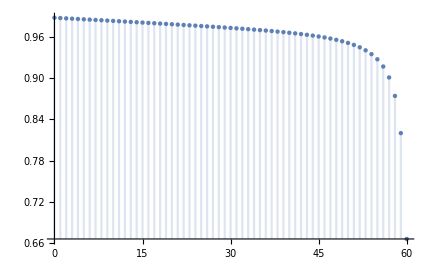

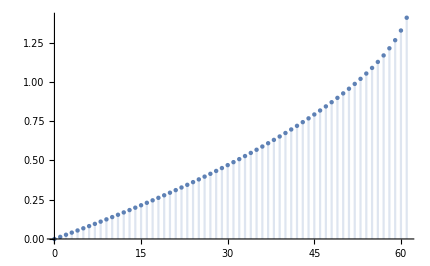

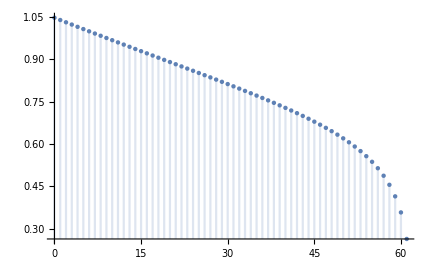

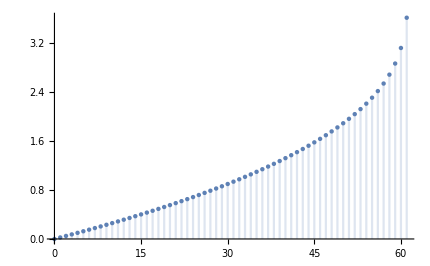

```mathematica
DiscretePlot[Hn[n]/Hn[n+1],{n,0,nMAX},PlotRange->All]
DiscretePlot[ϕ[n],{n,0,nMAX},PlotRange->All]
DiscretePlot[θ[n],{n,0,nMAX},PlotRange->All]
DiscretePlot[Subscript[p, θ][n],{n,0,nMAX},PlotRange->All]
```